```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
(*udata=ReadList["Geff.dat", {Number,Number}];
cdatah=ReadList["cdatah.txt",{Number,Number}];
*)
```

```mathematica
(*rudata=Join[udata,cdatah];*)
```

```mathematica
(*u=Interpolation[rudata];*)
ru[r_]:=Piecewise[{{1,0≤r<0.4},{4/3,0.4<=r≤48.90},{1,r>48.90}}];
```

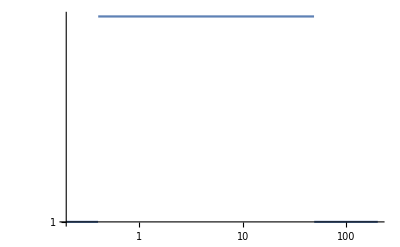

```mathematica
LogLogPlot[ru[r],{r,0,201.5}]
```

```mathematica
(*du=D[u[r],r];
rdu[r_]:=Piecewise[{{0,0≤r<0.01},{du,0.01<=r≤201.5},{0,r>201.5}}]*)
```

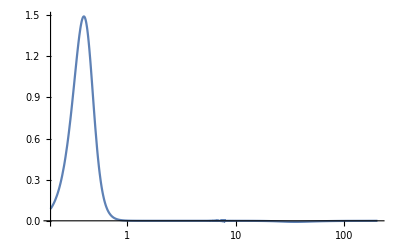

```mathematica
(*LogLinearPlot[rdu[r],{r,0,201.5},PlotRange->All]*)
```

```mathematica
(*rdudata=Table[{x,rdu[x]},{x,0,1,0.01}];
rduf=Interpolation[rdudata];
rrduf[r_]:=Piecewise[{{rduf[r],0<=r≤1},{0,r>1}}]*)
```

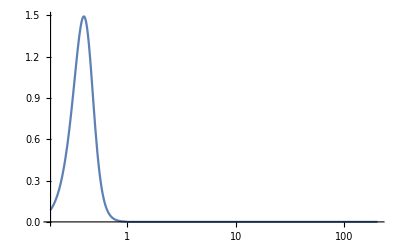

```mathematica
(*LogLinearPlot[rrduf[r],{r,0,201.5},PlotRange->All]*)
```

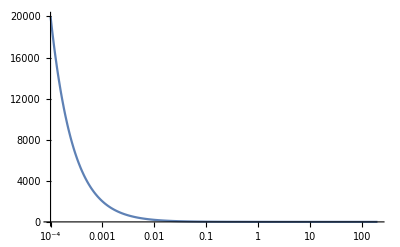

```mathematica
a1[b_]:=b*NIntegrate[((1+ru[r])*ru[r])/r^3/.r->√(b^2+z^2),{z,0,∞}]
LogLinearPlot[a1[b],{b,0.0001,201.5},PlotRange->All]
```

```mathematica
(*a2[b_]:=b*NIntegrate[((1+ru[r])*rdu[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a2[b],{b,0.0001,201.5},PlotRange->All]
*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363604}. NIntegrate obtained 5.0308 and 0.000485539 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363604}. NIntegrate obtained 2.65731 and 0.000254568 for the integral and error estimates.

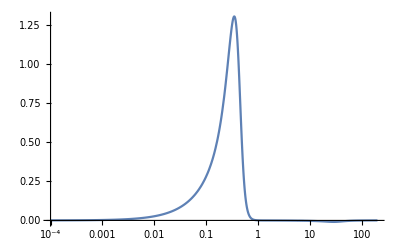

```mathematica
(*a3[b_]:=b*NIntegrate[(ru[r]*rdu[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a3[b],{b,0.0001,201.5},PlotRange->All]*)
```

```mathematica
Ibdata1=Table[{b,a1[b]},{b,0.001,1,0.001}];
Ibdata2=Table[{b,a1[b]},{b,1.01,201.5,0.01}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363554}. NIntegrate obtained 5.03082 and 0.000484801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363554}. NIntegrate obtained 2.65732 and 0.000254166 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.363403}. NIntegrate obtained 5.03095 and 0.000532808 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {7.59253}. NIntegrate obtained 0.000675049 and 0.0000277841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {7.59253}. NIntegrate obtained 0.000393811 and 0.0000158617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {7.86002}. NIntegrate obtained 0.000520056 and 0.0000252571 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Ibdata3=Table[{b,a1[b]},{b,0.00101,0.00199,0.00001}];
```

```mathematica
Ibdatan=Join[Ibdata1,Ibdata2,Ibdata3];
```

```mathematica
Ibdata=Sort[Ibdatan,#1[[1]]<#2[[1]]&];
```

```mathematica
Export["Ibdata.txt",Ibdata,"Table"];
```

```mathematica
Ibdata=ReadList["Ibdata.txt",{Number,Number}];
```

```mathematica
rIb=Interpolation[Ibdata];
```

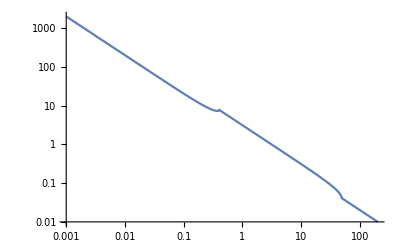

```mathematica
rrIb[b_]:=Piecewise[{{2/b,b<-201.5},{-rIb[-b],-201.5≤b≤-0.001},{2/b,-0.001<b<0.001},{rIb[b],0.001<=b≤201.5},{2/b,b>201.5}}];
LogLogPlot[rrIb[b],{b,0.001,201.5},PlotRange->All]
```

```mathematica
(*LogLogPlot[{a1[b]-a2[b]-a3[b],rrIb[b]},{b,0.01,110},PlotRange->All]*)
```

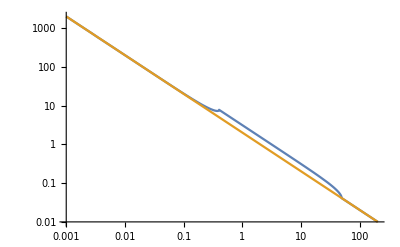

```mathematica
LogLogPlot[{rrIb[b],2/b},{b,0.001,201.5},PlotRange->All]
```

```mathematica
(*Itbdata=Table[{Ibdata[[i,1]],Ibdata[[i,2]]/Ibdata[[i,1]]},{i,1,Length[Ibdata]}];*)
```

```mathematica
(*Export["Itbdata.txt",Itbdata,"Table"];*)
```

```mathematica
Itbdata=ReadList["Itbdata.txt",{Number,Number}];
```

```mathematica
rItb=Interpolation[Itbdata];
```

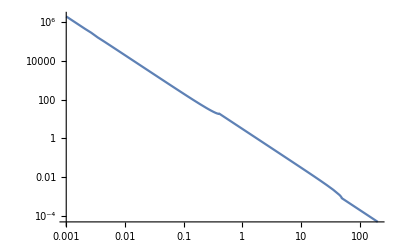

```mathematica
rrItb[b_]:=Piecewise[{{2/b^2,b<-201.5},{rItb[-b],-201.5≤b≤-0.001},{2/b^2,-0.001<b<0.001},{rItb[b],0.001<=b≤201.5},{2/b^2,b>201.5}}];
LogLogPlot[rrItb[b],{b,0.001,201.5},PlotRange->All]
```

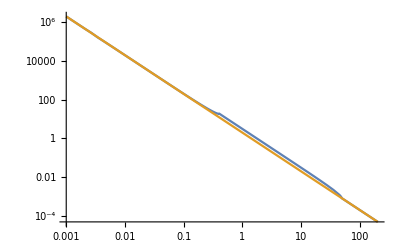

```mathematica
LogLogPlot[{rrItb[b],2/b^2},{b,0.001,201.5},PlotRange->All]
```

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=70;(*km s^-1 Mpc^-1*)
h0c=68;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^15;(*Msun*)
sigmav=900;(*km s^-1*)
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]
DA2[zl,zs]/(DA[zl]*DA[zs])

DAc[zl]
DAc[zs]
DA2c[zl,zs]
DA2c[zl,zs]/(DAc[zl]*DAc[zs])
```

919.403

1653.06

1055.45

0.000694452

946.444

1701.68

1086.49

0.00067461

```mathematica
thetaE=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs]
thetaEc=(4Pi*sigmav^2)/c^2*DA2c[zl,zs]/DAc[zs]
thetaE*DA[zl]
```

0.0000722105

0.0000722105

0.0663905

```mathematica
rhoSISGR[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/r^2;
```

```mathematica
SigmaSISGR[ksi_]:=sigmav^2/(2*G)*30.85678*10^18*1/ksi;
```

```mathematica
alphaSISGR[ksi_]:=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs];
```

```mathematica
alphaSISGR[ksi]
```

0.0000722105

```mathematica
rhoSISMG[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/(ru[r]*r^2);
```

```mathematica
SigmaSISMG[ksi_]:=2NIntegrate[rhoSISMG[r]/.r->(ksi^2+z^2)^(1/2),{z,0,Infinity}];
```

```mathematica
SigmaSISMGana[ksi_]:=Piecewise[{{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*(ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]-3/4*ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0<=ksi<0.4},{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*(3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0.4≤ksi≤48.9},{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*Pi/2,ksi>48.9}}];
```

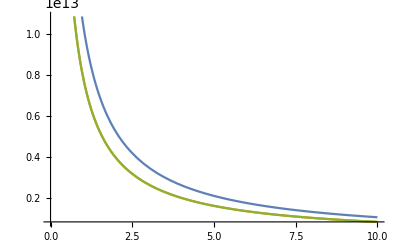

```mathematica
Plot[{SigmaSISGR[ksi],SigmaSISMG[ksi],SigmaSISMGana[ksi]},{ksi,0.001,10}]
```

```mathematica
ksiSigmaSISMGana[ksi_]:=Piecewise[{{sigmav^2/(Pi*G)*30.85678*10^18*(ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]-3/4*ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0<=ksi<0.4},{sigmav^2/(Pi*G)*30.85678*10^18*(3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0.4≤ksi≤48.9},{sigmav^2/(Pi*G)*30.85678*10^18*Pi/2,ksi>48.9}}];
```

```mathematica
alphaSISMG[ksi_]:=DA2[zl,zs]/DA[zs]*(2*G)/c^2*1/(30.85678*10^18)*NIntegrate[ksiSigmaSISMGana[ksip]*(ksi-ksip*Cos[phi])*rrItb[(ksi^2+ksip^2-2ksi*ksip*Cos[phi])^(1/2)],{phi,0,2Pi},{ksip,0,1000}];
```

```mathematica
alphaSISMG[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

9.65071×10^-6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {6.2831773838340207592151440314787169683086176519282162189483642578,0.00100017}. NIntegrate obtained 1.31554×10^16 and 6.46556×10^12 for the integral and error estimates.

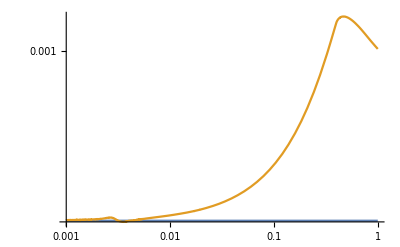

```mathematica
LogLogPlot[{alphaSISGR[ksi],alphaSISMG[ksi]},{ksi,0.001,1},PlotRange->All]
```

```mathematica
alphaSISMGdata1=Table[{ksi,alphaSISMG[ksi]},{ksi,0.0001,0.00099,0.00001}];
alphaSISMGdata2=Table[{ksi,alphaSISMG[ksi]},{ksi,0.001,0.0099,0.0001}];
alphaSISMGdata3=Table[{ksi,alphaSISMG[ksi]},{ksi,0.01,1,0.001}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.0909113}. NIntegrate obtained 1.31472×10^16 and 2.84726×10^12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.0991014}. NIntegrate obtained 1.31473×10^16+6.8479491268332981715371060302774047663503113918057432010536270707×10^-327 ⅈ and 1.68096×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.107143}. NIntegrate obtained 1.31474×10^16 and 1.68428×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.500003}. NIntegrate obtained 1.31569×10^16 and 1.28597×10^11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.500003}. NIntegrate obtained 1.31581×10^16-1.33418×10^-10 ⅈ and 4.13878×10^11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.499999}. NIntegrate obtained 1.31593×10^16 and 3.36445×10^11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.32371×10^16-2.24212×10^-11 ⅈ and 4.11241×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.500003}. NIntegrate obtained 1.32383×10^16+4.65111×10^-16 ⅈ and 9.42637×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.500003}. NIntegrate obtained 1.32493×10^16 and 9.15097×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.500003}. NIntegrate obtained 1.32601×10^16 and 8.6201×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.36292×10^16-4.08303×10^-12 ⅈ and 2.33081×10^10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.3649×10^16+2.90843×10^-7 ⅈ and 2.39433×10^10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.36588×10^16 and 2.06261×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

$Aborted

```mathematica
alphaSISMGdata4=Table[{ksi,alphaSISMG[ksi]},{ksi,0.00001,0.00009,0.00001}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.00990087}. NIntegrate obtained 1.31462×10^14 and 1.21136×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.0196076}. NIntegrate obtained 1.31463×10^14-3.2618×10^-18 ⅈ and 1.01317×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in phi near {phi,ksip} = {0.46602,0.000103042}. NIntegrate obtained 1.31464×10^14-0.176277 ⅈ and 3.49054×10^9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
alphaSISMGdata5=Table[{ksi,alphaSISMG[ksi]},{ksi,0.000001,0.000009,0.000001}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.000999059}. NIntegrate obtained 1.31462×10^14 and 2.5071×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.00199608}. NIntegrate obtained 1.31463×10^14 and 1.7987×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.00299107}. NIntegrate obtained 1.31467×10^14 and 2.70336×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
alphaSISMGdata6=Table[{ksi,alphaSISMG[ksi]},{ksi,1.1,10,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.00056717964854296609380939810939654090618339705409143033094306092271,4.10208}. NIntegrate obtained 1.53613×10^14 and 1.72533×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.00041115223553420992032977414896326680980835692980587630990823125818,6.10336}. NIntegrate obtained 1.51233×10^14 and 1.59819×10^8 for the integral and error estimates.

```mathematica
alphaSISMGdata7=Table[{ksi,alphaSISMG[ksi]},{ksi,10,500,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.40275×10^14 and 1.5934×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.33464×10^14 and 2.2125×10^8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.27165×10^14 and 2.79044×10^8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.90692×10^-6,0.0947946}. NIntegrate obtained 1.22872×10^14 and 2.09159×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.90692×10^-6,0.133697}. NIntegrate obtained 1.23463×10^14 and 2.40131×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999766932150860961396149047611392468581925641046836972236633301,0.169402}. NIntegrate obtained 1.2394×10^14 and 2.07835×10^8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
alphaSISMGdata=Join[alphaSISMGdata5,alphaSISMGdata4,alphaSISMGdata1,alphaSISMGdata2,alphaSISMGdata3];
```

```mathematica
Export["alphaSISMGdata.txt",alphaSISMGdata,"Table"]
```

alphaSISMGdata.txt

```mathematica
alphaSISMGdata=ReadList["alphaSISMGdata.txt",{Number,Number}];
```

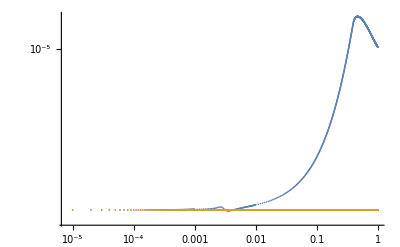

```mathematica
ListLogLogPlot[{alphaSISMGdata,Table[{x,8.023388938454735*^-6},{x,0,1,0.00001}]}]
```

```mathematica
alphaSISMGf=Interpolation[alphaSISMGdata];
```

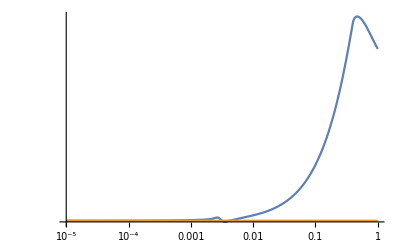

```mathematica
LogLogPlot[{9*alphaSISMGf[r],alphaSISGR[r]},{r,10^-5,1},PlotRange->All]
```

```mathematica
ralphaSISMGf[r_]:=Piecewise[{{-9*alphaSISMGf[-r],-1≤r≤-10^-5},{-9*8.023388938454735*^-6,-10^-5<r<0},{9*8.023388938454735*^-6,0≤r<10^-5},{9*alphaSISMGf[r],10^-5<=r<=1}}];
```

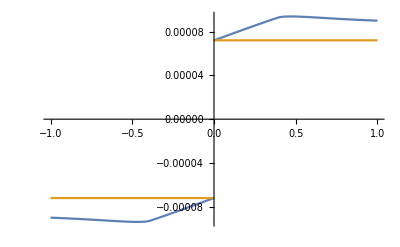

```mathematica
Plot[{ralphaSISMGf[r],alphaSISGR[r]*Sign[r]},{r,-1,1},PlotRange->All]
```

```mathematica
y=0.1;
```

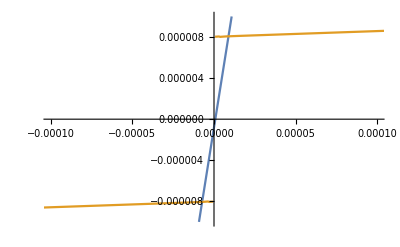

```mathematica
Plot[{theta-y*thetaE,ralphaSISMGf[DA[zl]*theta]},{theta,-10^-3,10^-3},PlotRange->{{-10^-4,10^-4},{-0.00001,0.00001}}]
```

```mathematica
n=2000;
```

```mathematica
thetaGRpd=Table[0,{n}];
thetaGRmd=Table[0,{n}];
thetaGRcpd=Table[0,{n}];
thetaGRcmd=Table[0,{n}];
thetaMGpd=Table[0,{n}];
thetaMGmd=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,y=0.0005*(i-1);
thetaGRp=y*thetaE+thetaE;
thetaGRm=y*thetaE-thetaE;
thetaGRpd[[i]]={y,thetaGRp};
thetaGRmd[[i]]={y,thetaGRm};
thetaGRcp=y*thetaE+thetaEc;
thetaGRcm=y*thetaE-thetaEc;
thetaGRcpd[[i]]={y,thetaGRcp};
thetaGRcmd[[i]]={y,thetaGRcm};
thetaMGp=theta/.FindRoot[theta-y*thetaE==ralphaSISMGf[DA[zl]*theta],{theta,thetaGRp}];
thetaMGm=theta/.FindRoot[theta-y*thetaE==ralphaSISMGf[DA[zl]*theta],{theta,thetaGRm}];
thetaMGpd[[i]]={y,thetaMGp};
thetaMGmd[[i]]={y,thetaMGm};]
```

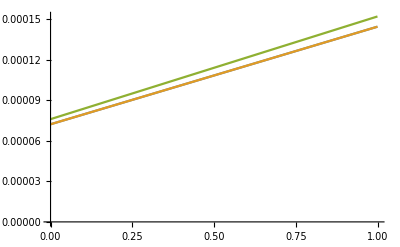

```mathematica
ListPlot[{thetaGRpd,thetaGRcpd,thetaMGpd},Joined->True,PlotRange->All]
```

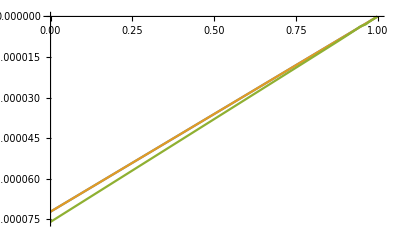

```mathematica
ListPlot[{thetaGRmd,thetaGRcmd,thetaMGmd},Joined->True,PlotRange->All]
```

```mathematica
min1=Min[Table[thetaGRpd[[i,2]],{i,1,n}],Table[thetaGRcpd[[i,2]],{i,1,n}],Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.0000722105

```mathematica
max1=Max[Table[thetaGRpd[[i,2]],{i,1,n}],Table[thetaGRcpd[[i,2]],{i,1,n}],Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.000151953

```mathematica
min2=Min[Table[thetaGRmd[[i,2]],{i,1,n}],Table[thetaGRcmd[[i,2]],{i,1,n}],Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-0.0000759963

```mathematica
max2=Max[Table[thetaGRmd[[i,2]],{i,1,n}],Table[thetaGRcmd[[i,2]],{i,1,n}],Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-3.61053×10^-8

```mathematica
Min[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

3.61053×10^-8

```mathematica
Max[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

0.000151953

```mathematica
phihGR[x_]:=thetaE*Abs[x];
phihGRc[x_]:=thetaEc*Abs[x];
phihMGini[x_]=yy[x]/.NDSolve[{yy'[theta]==ralphaSISMGf[DA[zl]*theta],yy[0.0000162]==0},yy,{theta,3.6*10^-8,0.000152},Method->"ExplicitRungeKutta"][[1]];
phihMG[x_]=phihMGini[Abs[x]];
```

```mathematica
TDGR=Table[0,{n}];
TDGRc=Table[0,{n}];
TDMG=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,thetaGRp=thetaGRpd[[i,2]];y=thetaGRpd[[i,1]];thetaGRm=thetaGRmd[[i,2]];
DettGR=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2(thetaGRp^2-thetaGRm^2));
TDGR[[i]]={y,DettGR};

thetaGRcp=thetaGRcpd[[i,2]];y=thetaGRcpd[[i,1]];thetaGRcm=thetaGRcmd[[i,2]];
DettGRc=(1+zl)/c*30.85678*10^18*(DAc[zl]*DAc[zs])/DA2c[zl,zs](1/2(thetaGRcp^2-thetaGRcm^2));
TDGRc[[i]]={y,DettGRc};
thetaMGp=thetaMGpd[[i,2]];y=thetaMGpd[[i,1]];thetaMGm=thetaMGmd[[i,2]];
alphaMGp=thetaMGp-y*thetaE;
alphaMGm=thetaMGm-y*thetaE;
DettMG=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2 alphaMGm^2-1/2 alphaMGp^2-(phihMG[thetaMGm]-phihMG[thetaMGp]));
TDMG[[i]]={y,DettMG};]
```

```mathematica
(*TDMG=ReadList["TDMG.txt",{Number,Number}];*)
```

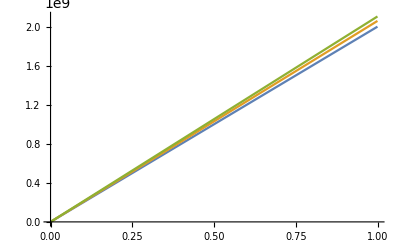

```mathematica
ListPlot[{TDGR,TDGRc,TDMG},Joined->True,PlotRange->All]
```

```mathematica
diffhc=Table[{TDGR[[i,1]],(TDGRc[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
diffMG=Table[{TDGR[[i,1]],(TDMG[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
(*diffMGc=Table[{TDGRt[[i,1]],(TDMGt[[i,2]]-TDGRct[[i,2]])},{i,1,Length[TDMGt]}];*)
```

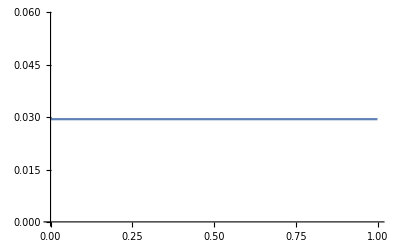

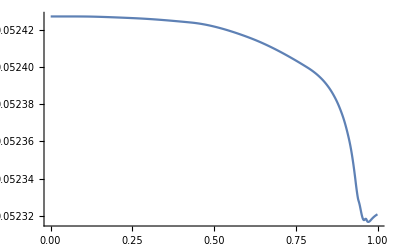

```mathematica
ListLinePlot[diffhc]
ListLinePlot[diffMG]
(*ListLinePlot[diffMGc]*)
```

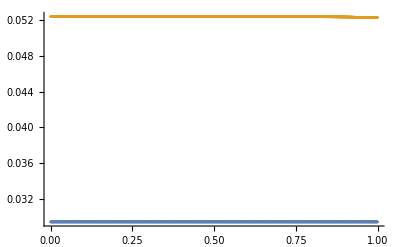

```mathematica
ListPlot[{diffhc,diffMG},PlotRange->All]
```

```mathematica
Export["thetaGRpd.txt",thetaGRpd,"Table"];
Export["thetaGRcpd.txt",thetaGRcpd,"Table"];
Export["thetaMGpd.txt",thetaMGpd,"Table"];
Export["thetaGRmd.txt",thetaGRmd,"Table"];
Export["thetaGRcmd.txt",thetaGRcmd,"Table"];
Export["thetaMGmd.txt",thetaMGmd,"Table"];
```

```mathematica
Export["TDGR.txt",TDGR,"Table"];
Export["TDGRc.txt",TDGRc,"Table"];
Export["TDMG.txt",TDMG,"Table"];
```